# CatalanUnrank

Find the totally balanced binary sequence for a given rank

## DefinitionDefinitionDefine your function using the name you gave in the Title line above. You can add input cells and extra code to define additional input cases or prerequisites. All definitions, including dependencies, will be included in the generated resource function. This section should be evaluated before creating the Examples section below.

```mathematica
CatalanUnrank[n_,rank_]:= 
Module[{ lo=0,y=0, a=Table[0,2 n],m},
Do[
m=Binomial[2 n -x, n-(x+y+1)/2]-Binomial[2 n -x, n-1-(x+y+1)/2];
(*these terms make the Catalan triangle, or ballot numbers*)
If[rank≤ lo+m-1,
y=y+1;
a[[x]]=0,
lo=lo+m;
y=y-1;
a[[x]]=1],
{x,1,2 n}];
a]
```

## Documentation

### UsageUsageDocument input usage cases by first typing an input structure, then pressing to add a brief explanation of the function’s behavior for that structure. Pressing repeatedly will create new cases as needed. Every input usage case defined above should be demonstrated explicitly here. See existing documentation pages for examples.

CatalanUnrank[n,rank]

gives the totally balanced binary sequence with n ones and the given rank.

### Details & OptionsDetails & OptionsGive a detailed explanation of how the function is used and configured (e.g. acceptable input types, result formats, options specifications, background information). This section may include multiple cells, bullet lists, tables, hyperlinks and additional styles/structures as needed. Add any other information that may be relevant, such as when the function was first discovered or how and why it is used within a given field. Include all relevant background or contextual information related to the function, its development, and its usage.

A binary sequence is considered totally balanced if the number of zeros is at least as large as the number of ones as one progresses from left to right in a list of zeros and ones, and the total counts are equal (implying the first element must be zero and the last element one).

For n ones there are C_n totally balanced binary sequences, where C_n is the Catalan number.

The value returned is the member at position rank in the set of all possible balanced sequences with n zeros and n ones, ordered according to a certain enumeration scheme.

Given a balanced sequence of zeros and ones, its position in the enumeration of all such can be found using the resource function CatalanRank.

Brackets in a computer program must be balanced. One can think of a proper bracketing as having left brackets corresponding to zeros and right brackets to ones in a balanced binary sequence.

## ExamplesExamplesDemonstrate the function’s usage, starting with the most basic use case and describing each example in a preceding text cell. Within a group, individual examples can be delimited by inserting page breaks between them (either using "[Right-click]"" ▶ ""Insert Page Break" between cells or through the menu using "Insert"" ▶ ""Page Break"). Examples should be grouped into Subsection and Subsubsection cells similarly to existing documentation pages. Here are some typical Subsection names and the types of examples they normally contain: "◼ ""Basic Examples: "most basic function usage "◼ ""Scope: "input and display conventions, standard computational attributes (e.g. threading over lists) "◼ ""Options: "available options and parameters for the function "◼ ""Applications: "standard industry or academic applications "◼ ""Properties and Relations: "how the function relates to other functions "◼ ""Possible Issues: "limitations or unexpected behavior a user might experience "◼ ""Neat Examples: "particularly interesting, unconventional, or otherwise unique usage

### Basic Examples

Find the 20th totally balanced binary sequence with five 1's:

```mathematica
CatalanUnrank[5,20]
```

{0,0,1,0,1,0,1,1,0,1}

Find the number of totally balanced binary sequences with five 1's:

```mathematica
CatalanNumber[5]
```

42

Show the totally balanced binary sequences with five 1’s:

```mathematica
CatalanUnrank[5,#]&/@Range[0,CatalanNumber[5]-1]
```

{{0,0,0,0,0,1,1,1,1,1},{0,0,0,0,1,0,1,1,1,1},{0,0,0,0,1,1,0,1,1,1},{0,0,0,0,1,1,1,0,1,1},{0,0,0,0,1,1,1,1,0,1},{0,0,0,1,0,0,1,1,1,1},{0,0,0,1,0,1,0,1,1,1},{0,0,0,1,0,1,1,0,1,1},{0,0,0,1,0,1,1,1,0,1},{0,0,0,1,1,0,0,1,1,1},{0,0,0,1,1,0,1,0,1,1},{0,0,0,1,1,0,1,1,0,1},{0,0,0,1,1,1,0,0,1,1},{0,0,0,1,1,1,0,1,0,1},{0,0,1,0,0,0,1,1,1,1},{0,0,1,0,0,1,0,1,1,1},{0,0,1,0,0,1,1,0,1,1},{0,0,1,0,0,1,1,1,0,1},{0,0,1,0,1,0,0,1,1,1},{0,0,1,0,1,0,1,0,1,1},{0,0,1,0,1,0,1,1,0,1},{0,0,1,0,1,1,0,0,1,1},{0,0,1,0,1,1,0,1,0,1},{0,0,1,1,0,0,0,1,1,1},{0,0,1,1,0,0,1,0,1,1},{0,0,1,1,0,0,1,1,0,1},{0,0,1,1,0,1,0,0,1,1},{0,0,1,1,0,1,0,1,0,1},{0,1,0,0,0,0,1,1,1,1},{0,1,0,0,0,1,0,1,1,1},{0,1,0,0,0,1,1,0,1,1},{0,1,0,0,0,1,1,1,0,1},{0,1,0,0,1,0,0,1,1,1},{0,1,0,0,1,0,1,0,1,1},{0,1,0,0,1,0,1,1,0,1},{0,1,0,0,1,1,0,0,1,1},{0,1,0,0,1,1,0,1,0,1},{0,1,0,1,0,0,0,1,1,1},{0,1,0,1,0,0,1,0,1,1},{0,1,0,1,0,0,1,1,0,1},{0,1,0,1,0,1,0,0,1,1},{0,1,0,1,0,1,0,1,0,1}}

### Neat Examples

The first few balanced binary sequences of rank 40:

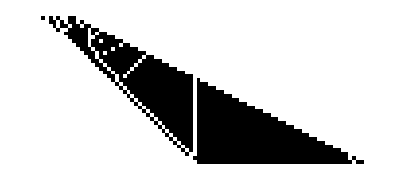

```mathematica
ArrayPlot[Table[CatalanUnrank[n,40],{n,5,42}]]
```

## Source & Additional Information

### Contributed ByContributed ByEnter the name of the person, people or organization that should be publicly credited with contributing this function.

Ed Pegg Jr

### KeywordsKeywordsList relevant terms (e.g. functional areas, algorithm names, related concepts) that should be used to include the function in search results.

Catalan

Indexing

Rank

matched bracketing

### Categories

Cloud & Deployment |  Core Language & Structure
 Data Manipulation & Analysis |  Engineering Data & Computation
 External Interfaces & Connections |  Financial Data & Computation
 Geographic Data & Computation |  Geometry
 Graphs & Networks |  Higher Mathematical Computation
 Images |  Just For Fun
 Knowledge Representation & Natural Language |  Machine Learning
 Notebook Documents & Presentation |  Programming Utilities
 Repository Tools |  Scientific and Medical Data & Computation
 Social, Cultural & Linguistic Data |  Sound
 Strings & Text |  Symbolic & Numeric Computation
 System Operation & Setup |  Time-Related Computation
 User Interface Construction |  Visualization & Graphics
 Wolfram Physics Project |

### Related SymbolsRelated SymbolsList up to twenty documented, system-level Wolfram Language symbols related to the function.

CatalanNumber

### Related Resource ObjectsRelated Resource ObjectsList the names of published resource objects from any Wolfram repository that are related to this function.

CatalanRank

### Source/Reference CitationSource/Reference CitationGive a bibliographic-style citation for the original source of the function and/or its components (e.g. a published paper, algorithm, or code repository).

Source, reference or citation information

### LinksLinksList additional URLs or hyperlinks for external information related to the function.

Link to other related material

### TestsTestsSpecify an optional list of tests for verifying that the function is working properly in any environment. Tests can be specified as Input/Output cell pairs or as symbolic VerificationTest expressions for including additional options.

```mathematica
MyFunction[x,y]
```

x y

## Author Notes

Additional information about limitations, issues, etc.

## Submission NotesSubmission NotesEnter any additional information that you would like to communicate to the reviewer here. This section will not be included in the published resource.

Additional information for the reviewer.